```mathematica
Mixing (one res, one bound)
```

## DEFINE PARAMTERS

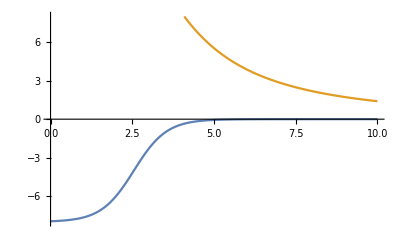

```mathematica
Subscript[m, N]=940;ℏc=197.327;
V0=8;R=2.55;a=0.5;μ=8/9 Subscript[m, N];
E2=3;
rmax=10.;dr=0.01;
rlist=Range[dr,rmax,dr];
len=Length[rlist];
Vwoods[r_]:=-V0/(1+Exp[(r-R)/a]);
Vcent[r_,l_]:=(l(l+1)ℏc^2)/(2μ r^2);
V00[r_]:=Vwoods[r]+Vcent[r,0];
V22[r_]:=Vwoods[r]+Vcent[r,2];
V00mat=DiagonalMatrix[V00[rlist]];
V22mat=DiagonalMatrix[V22[rlist]];
(*MIXING*)
V02mat=V20mat=DiagonalMatrix[Vwoods[rlist]];
(*INITIAL HAMILTONIAN*)
one[n_,d_]:=
DiagonalMatrix[1+0Range[n-Abs[d]],d];
H000:=V00mat+-ℏc^2/(2 μ) 1/dr^2(one[len,-1]-2 one[len,0]+one[len,1]);
H022:=V22mat+-ℏc^2/(2 μ) 1/dr^2(one[len,-1]-2 one[len,0]+one[len,1])+E2;
H0:=ArrayFlatten[{{H000,V02mat},{V20mat,H022}}];
ListLinePlot[{V00[rlist],V22[rlist]},DataRange->{dr,rmax},PlotRange->{-V0,V0}]
```

## SOLUTIONS

```mathematica
(*DEFINITIONS*)
```

```mathematica
k0[En_?NumericQ]:=Sqrt[(2μ En)/ℏc^2];
k2[En_?NumericQ]:=Sqrt[(2μ (En-E2))/ℏc^2];
wave0[En_,r_]:=SphericalHankelH1[0,k0[En] r];
wave2[En_,r_]:=SphericalHankelH1[2,k2[En] r];
B0[En_]:=rmax/wave0[En,rmax](D[wave0[En,r],r]/.r->rmax);
B2[En_]:=rmax/wave2[En,rmax](D[wave2[En,r],r]/.r->rmax);
(*HAMILTONIAN*)
Hnew[En_]:=Module[{H=H0},H[[len,len]]=V00mat[[len,len]]+-ℏc^2/(2 μ) 1/dr^2(dr B0[En]/rmax-1);H[[2 len,2 len]]=V22mat[[len,len]]+-ℏc^2/(2 μ) 1/dr^2(dr B2[En]/rmax-1);H];
(*RETURNS EIGEMVALUE*)
ϵ=10^-5;
n=1;
evals=List[];evecs=List[];
eigenv[{En_?NumericQ,i_}]:=({eval,evec}=Transpose@SortBy[Transpose[Eigensystem[Hnew[En]]],First];{eval[[i]],i});
```

```mathematica
(*RETURNS EIGENSYSTEM*)
(*En=x/.FindRoot[Im[eigenvres1[x,n,l]]==Im[x],{x,0.1+0.I,0.,V0}]//Timing*)
En=NestWhileList[eigenv,{0,n},Abs[Abs[#1[[1]]]-Abs[#2[[1]]]]>ϵ&,2,100][[-1,1]];
evals=Append[evals,En];evecs=Append[evecs,evec[[n]]];
```

```mathematica
eigenv[{0,1}]
```

{-0.0594713+0. ⅈ,1}

```mathematica
eigenv[%]
```

{0.209918+0. ⅈ,1}

```mathematica
eigenv[%]
```

{0.174049-0.138167 ⅈ,1}

```mathematica
eigenv[%]
```

{0.101357-0.154149 ⅈ,1}

```mathematica
eigenv[%]
```

{0.0745513-0.140043 ⅈ,1}

```mathematica
eigenv[%]
```

{0.0687038-0.127512 ⅈ,1}

```mathematica
eigenv[%]
```

{0.0701601-0.120981 ⅈ,1}

```mathematica
eigenv[%]
```

{0.0727435-0.118909 ⅈ,1}

```mathematica
eigenv[%]
```

{0.0743863-0.118934 ⅈ,1}

```mathematica
eigenv[%]
```

{0.0750011-0.119464 ⅈ,1}

```mathematica
eigenv[%]
```

{0.0750651-0.119859 ⅈ,1}

```mathematica
eigenv[%]
```

{0.0749645-0.120028 ⅈ,1}

```mathematica
eigenv[%]
```

{0.0748733-0.12006 ⅈ,1}

```mathematica
eigenv[%]
```

{0.0748288-0.120043 ⅈ,1}

```mathematica
eigenv[%]
```

{0.0748173-0.120023 ⅈ,1}

```mathematica
(*MATCHES AMPLITUDE & PLOTS*)
const0[i_]:=evec[[i,-len-1]]/wave0[eval[[i]],rmax,δ];
const2[i_]:=evec[[i,-1]]/wave2[eval[[i]],rmax];
rmaxx=20.;
```

```mathematica
i=1;
ListLinePlot[{Transpose[{rlist,Part[evecs[[i]],1;;len]}],Transpose[{rlist,Part[evecs[[i]],len+1;;2 len]}],Transpose[{Range[rmax,rmaxx,dr], const0[i] wave0[evals[[i]],Range[rmax,rmaxx,dr]]}],Transpose[{Range[rmax,rmaxx,dr], const2[i] wave2[evals[[i]],Range[rmax,rmaxx,dr]]}]},PlotRange->All]
```